```mathematica
ClearAll["Global`*"]
```

# gsl

If you want to properly embed this package into mathematica, then follow these steps:

1) run

```mathematica
SystemOpen[$UserBaseDirectory<>"/Applications"]
```

2) copy and paste gsl.wl into the Applications folder

3) Get the package by running <<gsl`

Alternatively, the following also works so long as you have gsl.wl in the notebooks directory

```mathematica
SetDirectory[NotebookDirectory[]]
<<gsl`
```

/Users/alexanderpickston/Documents/GitHub/QIPmma/Graph states

gsl library has been loaded successfully. Have fun!

```mathematica
?gsl`*
```

## Using function library

### Functions

#### CustomGraph

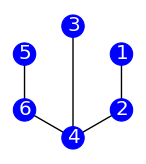

```mathematica
g=CustomGraph[{{1,2},{2,4},{4,3},{4,6},{6,5}}]
```

#### LCQubit

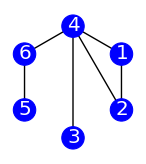

```mathematica
LC2=LCQubit[g,2]
```

#### LCOrbit

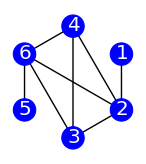
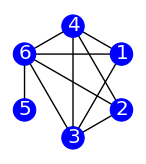
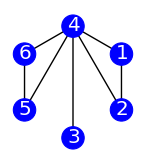
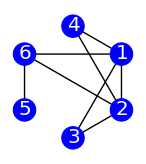
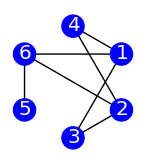
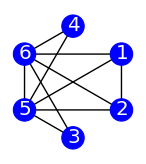
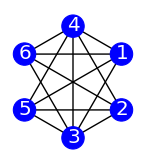
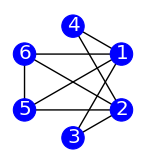
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LCOrbit[g]
```

#### Zmeasurement

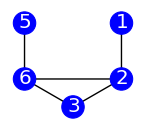

```mathematica
Zmeasurement[-Graphics-,4]
```

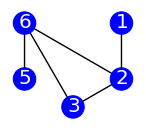
```mathematica
Zmeasurement[-Graphics-,1]
```

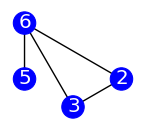

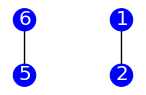

```mathematica
Zmeasurement[g,4]
```

#### Ymeasurement

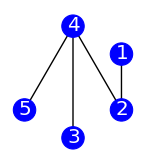

```mathematica
Ymeasurement[g,6]
```

#### Xmeasurement

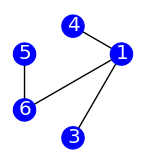

```mathematica
Xmeasurement[g,2]
```

#### FindStabilizers

```mathematica
state=(1/Sqrt[2])*(Kron[h,h,h,h]+Kron[v,v,v,v])
```

{{1/(√2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√2)}}

```mathematica
FindStabilzers[state]//TableForm
```

𝕀[1] | 𝕀[2] | 𝕀[3] | 𝕀[4]
𝕀[1] | 𝕀[2] | ℤ[3] | ℤ[4]
𝕀[1] | 𝕀[2] | -ℤ[3] | -ℤ[4]
𝕀[1] | ℤ[2] | 𝕀[3] | ℤ[4]
𝕀[1] | ℤ[2] | ℤ[3] | 𝕀[4]
𝕀[1] | -ℤ[2] | 𝕀[3] | -ℤ[4]
𝕀[1] | -ℤ[2] | -ℤ[3] | 𝕀[4]
𝕏[1] | 𝕏[2] | 𝕏[3] | 𝕏[4]
ℤ[1] | 𝕀[2] | 𝕀[3] | ℤ[4]
ℤ[1] | 𝕀[2] | ℤ[3] | 𝕀[4]
ℤ[1] | ℤ[2] | 𝕀[3] | 𝕀[4]
ℤ[1] | ℤ[2] | ℤ[3] | ℤ[4]
ℤ[1] | ℤ[2] | -ℤ[3] | -ℤ[4]
ℤ[1] | -ℤ[2] | ℤ[3] | -ℤ[4]
ℤ[1] | -ℤ[2] | -ℤ[3] | ℤ[4]
-ℤ[1] | 𝕀[2] | 𝕀[3] | -ℤ[4]
-ℤ[1] | 𝕀[2] | -ℤ[3] | 𝕀[4]
-ℤ[1] | ℤ[2] | ℤ[3] | -ℤ[4]
-ℤ[1] | ℤ[2] | -ℤ[3] | ℤ[4]
-ℤ[1] | -ℤ[2] | 𝕀[3] | 𝕀[4]
-ℤ[1] | -ℤ[2] | ℤ[3] | ℤ[4]
-ℤ[1] | -ℤ[2] | -ℤ[3] | -ℤ[4]

#### FindGraph

```mathematica
FindGraph[state]//TableForm
```

𝕀[1]
𝕀[2]
𝕏[3]
ℤ[4] | 𝕀[1]
𝕏[2]
𝕀[3]
ℤ[4] | ℤ[1]
ℤ[2]
ℤ[3]
𝕏[4] | 𝕏[1]
𝕀[2]
𝕀[3]
ℤ[4]
𝕀[1]
𝕀[2]
ℤ[3]
𝕏[4] | 𝕀[1]
𝕏[2]
ℤ[3]
𝕀[4] | ℤ[1]
ℤ[2]
𝕏[3]
ℤ[4] | 𝕏[1]
𝕀[2]
ℤ[3]
𝕀[4]
𝕀[1]
ℤ[2]
𝕀[3]
𝕏[4] | 𝕀[1]
ℤ[2]
𝕏[3]
𝕀[4] | ℤ[1]
𝕏[2]
ℤ[3]
ℤ[4] | 𝕏[1]
ℤ[2]
𝕀[3]
𝕀[4]

#### DrawGraph

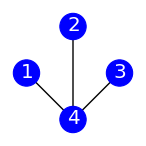
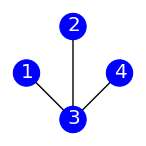
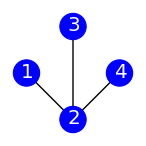

```mathematica
DrawGraph/@FindGraph[state]
```